```mathematica
Needs["ExperimentEvaluation`"]
SetDirectory["~"];
solverRewrite={"SOLVER",{"GP"->"G","NEAT"->"N"}};
distanceRewrite={"GP.DISTANCE",{"GENERAL"->"G","BASIC"->"I","ISO"->"D","PHENO"->"P","RANDOM"->"R","NODES"->"N","Null"->""}};
plotRange={All,{0,100}};
functionImplRewrite={"gpat.ATFunctions$"->"N","gpat.ATFunctionsNoConsts$"->"NC","gpat.ATFunctionsLikeGP$"->"GP","gpat.ATFunctionsLocks$"->"L","gpat.ATFunctionsComplexifyOnly$"->"CO","gpat.ATFunctionsAllConsts$"->"AC"};
```

## OCTOPUS Evolution

```mathematica
Needs["PlotLegends`"]
readRunFitness[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
readRunEvaluationInfo[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
data = Rest[allData];
{data,Max/@data, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
enlarge[list_, fill_, stat_]:=list~Join~Array[fill&,Max[Length/@stat]-Length[list]]
enlarge[list_, fill_, stat_, len_]:=list~Join~Array[fill&,len-Length[list]]
enlarge[list_,bsfAvg_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
bsfAvgGP = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/T/OCTOPUS/GP"}]);
(*bsfAvgGPEFSB = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/GPEFS_OCTOPUS_BASIC"}]);
bsfAvgGPEFSI = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/GPEFS_OCTOPUS_ISO"}]);
bsfAvgGPEFSR = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/GPEFS_OCTOPUS_RANDOM"}]);*)
bsfAvgGPEFSG = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/T/OCTOPUS/E_G"}]);
bsfAvgGPATG = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/T/OCTOPUS/AT_G"}]);
bsfAvgGPATB = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/T/OCTOPUS/AT_B"}]);
bsfAvgANJI = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/T/OCTOPUS/ANJI"}]);
(*bsfAvgNEAT = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/NEAT_OCTOPUS"}]);*)
```

```mathematica
maxGenerations=Max@@(Max[Length[#]&/@#]&/@{bsfAvgGP,bsfAvgANJI})
```

500

```mathematica
maxFitness=75000;
bsfAvgGP=Mean[bsfAvgGP]/maxFitness;
(*bsfAvgGPEFSB=Mean[bsfAvgGPEFSB];*)
(*bsfAvgGPEFSI=Mean[bsfAvgGPEFSI];*)
bsfAvgGPEFSG=Mean[bsfAvgGPEFSG]/maxFitness;
(*bsfAvgGPEFSR=Mean[bsfAvgGPEFSR];*)
bsfAvgGPATG=Mean[bsfAvgGPATG]/maxFitness;
bsfAvgGPATB=Mean[bsfAvgGPATB]/maxFitness;
bsfAvgANJI=Mean[bsfAvgANJI]/maxFitness;
(*bsfAvgNEAT=Mean[bsfAvgNEAT];*)
```

```mathematica
ListPlot[{bsfAvgANJI,bsfAvgGP,bsfAvgGPEFSG,bsfAvgGPATB}, PlotRange->{0.0,1},AspectRatio->1/GoldenRatio, AxesLabel->{"Generation","Fitness\n"},LabelStyle->Directive[FontSize->20],ImageSize->800,FrameTicks->{Automatic,Table[{i/10,ToString[10i]~~"%"},{i,2,11,2}]},Frame->True,
ImagePadding->{{70,5},{50,20}},PlotRangeClipping->False,
Epilog->{
Text[Style["generation",20],{250,-0.07}],
Rotate[Text[Style["fitness",20],{-50,0.5}],90 Degree]
},
GridLines->{{40},None},
GridLinesStyle->Orange
]
```

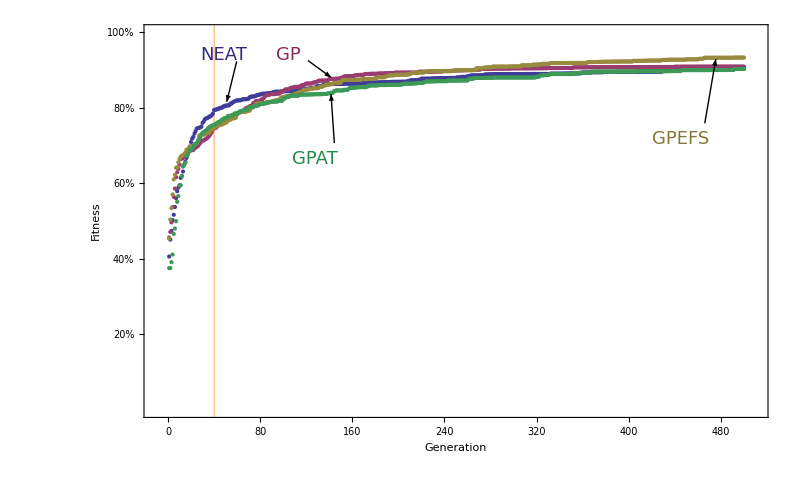
```mathematica
evoplot=-Graphics-
```

```mathematica
ANJI modra, GP FIALOVA, GPEFS zluta, GPAT zelena
```

### Statistical Tests for generation 40

```mathematica
bsfAvgGPATB = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/T/OCTOPUS/AT_B"}]);
bsfAvgANJI = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/T/OCTOPUS/ANJI"}]);
```

```mathematica
gpat40=bsfAvgGPATB[[All,40]]/maxFitness
```

{0.784573,0.840853,0.7824,0.74824,0.71884,0.811093,0.8056,0.758133,0.709307,0.701427,0.786187,0.71072,0.716813,0.724053,0.731467,0.784533,0.743307,0.731413,0.71268,0.789347}

```mathematica
anji40=bsfAvgANJI[[All,40]]/maxFitness
```

{0.80564,0.759733,0.744493,0.88952,0.855547,0.75232,0.819787,0.779267,0.825067,0.856813,0.74572,0.894907,0.78276,0.745813,0.78876,0.755013,0.773493,0.81688,0.65572,0.831587}

```mathematica
Mean[anji40]-Mean[gpat40]
```

0.0393927

```mathematica
MannWhitneyTest[{anji40,gpat40},Automatic,"PValueTable"]
```

| P-Value
Mann-Whitney | 0.0143638

### Statistical Tests for generation 500

```mathematica
bsfAvgGPEFSG = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/T/OCTOPUS/E_G"}]);
bsfAvgGP = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/T/OCTOPUS/GP"}]);
bsfAvgANJI = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/T/OCTOPUS/ANJI"}]);
```

```mathematica
gpefs500=bsfAvgGPEFSG[[All,-1]]/maxFitness
```

{0.9368,0.916373,0.916333,0.970493,0.902573,0.875507,0.946227,0.939,0.95756,0.883827,0.970067,0.934853,0.969133,0.9364,0.929853,0.970093,0.93344,0.945573,0.974147,0.850493}

```mathematica
gp500=bsfAvgGP[[All,-1]]/maxFitness
```

{0.920813,0.87808,0.893013,0.89744,0.87712,0.96116,0.931187,0.944467,0.959747,0.859547,0.896893,0.96956,0.888387,0.891107,0.918053,0.91152,0.917293,0.852573,0.935267,0.877933}

```mathematica
anji500=bsfAvgANJI[[All,-1]]/maxFitness
```

{0.892613,0.945467,0.912907,0.92292,0.92464,0.904467,0.90292,0.89456,0.88512,0.94724,0.866613,0.919813,0.87236,0.853973,0.881267,0.894653,0.89556,0.884613,0.932573,0.924893}

```mathematica
MannWhitneyTest[{gpefs500,gp500},Automatic,"PValueTable"]
```

| P-Value
Mann-Whitney | 0.0294409

```mathematica
MannWhitneyTest[{anji500,gp500},Automatic,"TestConclusion"]
```

The null hypothesis that the median difference is 0 is not rejected at the 5. percent level based on the Mann-Whitney test.

## OCTOPUS BSF

```mathematica
names={"T/OCTOPUS/ANJI","T/OCTOPUS/GP","T/OCTOPUS/E_G","T/OCTOPUS/E_B","T/OCTOPUS/AT_G","T/OCTOPUS/AT_B"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
(*data=data/.Join[functionImplRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];*)
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = data;
sortedData=replaceLabels[sortedData,{"NEAT","GP","GPEFS\nG","GPEFS\nI","GPAT\nG","GPAT\nI"}];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","PROBLEM","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}]
```

{GPAT.DISTANCE,GP.DISTANCE,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.MAX_DEPTH,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TYPE,OCTOPUS.SHOW_GRAPHICS,PARALLEL.FORCE_THREADS,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.progressShowHyperNet,PRINT.progressShowProblem,SOLVER,STORE_GENOTYPES_MATHEMATICA}

ID | PARAM FILE | SOLVER | ID | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | PROBLEM | SYMBOLIC_REGRESSION.F | GP.DISTANCE_GENERAL_K | GP.DISTANCE_GENERAL_DESCEND_NULL_TREES | GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT | MAZE.MAP
NEAT | T/OCTOPUS/ANJI/parameters_001.txt | ANJI | OCTOPUS |  |  | OCTOPUS |  |  |  |  | 
GP | T/OCTOPUS/GP/parameters_001.txt | GP | OCTOPUS |  |  | OCTOPUS |  | 1. | true | false | 
GPEFS
G | T/OCTOPUS/E_G/parameters_001.txt | GP | OCTOPUS |  |  | OCTOPUS |  | 1. | true | false | 
GPEFS
I | T/OCTOPUS/E_B/parameters_001.txt | GP | OCTOPUS |  |  | OCTOPUS |  | 1. | true | false | 
GPAT
G | T/OCTOPUS/AT_G/parameters_001.txt | GPAT | OCTOPUS | GENERAL | gpat.ATFunctionsAllConsts$ | OCTOPUS |  | 1. | false | false | 
GPAT
I | T/OCTOPUS/AT_B/parameters_001.txt | GPAT | OCTOPUS | BASIC | gpat.ATFunctionsAllConsts$ | OCTOPUS |  |  |  |  |

{{80,80%},{85,85%},{90,90%},{95,95%},{100,100%}}

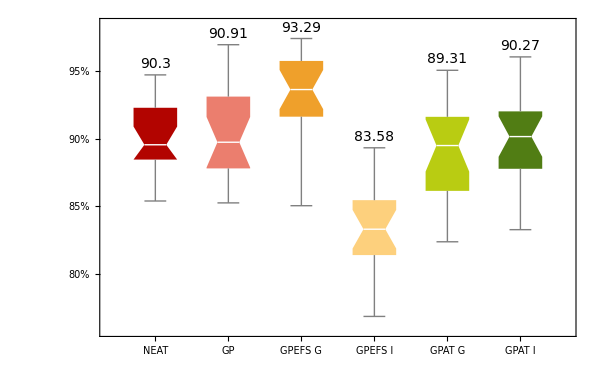

```mathematica
selectedData=sortedData/.{("BSF"->x:_)->("BSF"->x/750)};
epilog={
Text[Style[Grid[{{"Algorithm\nDistance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{0.2,73.6}],
Rotate[Text[Style["fitness",20],{-0.5,87.5}],90 Degree]
};
ticks=Table[{i,ToString[i]~~"%"},{i,80,100,5}]
plotAsBoxWhiskerChartPub[selectedData,"BSF",{},2.0,Length[selectedData],
ImagePadding->{{70,5},{45,25}},ImageSize->600,PlotRange->{All,{Automatic,100}},
ColorsNumber->6,
AspectRatio->1/GoldenRatio,
RoundMeansTo->0.01,
Epilog->epilog,
FrameTicks->{{ticks,None},{None,None}}]
```

```mathematica
Export["bsf_fitness.pdf",%];
```